Import  all variability data  for each GPU

We  changed  the definition of the variability so we need to apply a correction to the data.

```mathematica
SetDirectory["/home/mathieut/Projects/codes/correctness/Data"];
NumElements={10,100,1000,10000,100000,1000000};
ApplyCorrection[table_]:=Module[{tmp,ls}, 
tmp=Flatten[table];
ls=Dimensions[table];
Return[
Partition[
Partition[Map[1-Abs[1+#]&,tmp],ls[[3]]],
ls[[2]]]
];
]
V100data=ApplyCorrection[{Map[Drop[#,1]&,Import["Data/V100/relative_error_block_reduction_V100_normal.csv.bz2"]],Map[Drop[#,1]&,Import["Data/V100/relative_error_block_reduction_V100_uniform.csv.bz2"]],Map[Drop[#,1]&,Import["Data/V100/relative_error_block_reduction_V100_uniform_centered.csv.bz2"]]}];
Mi250Xdata=ApplyCorrection[{Map[Drop[#,1]&,Import["Data/Mi250X/relative_error_block_reduction_Mi250X_normal.csv.bz2"]],Map[Drop[#,1]&,Import["Data/Mi250X/relative_error_block_reduction_Mi250X_uniform.csv.bz2"]],Map[Drop[#,1]&,Import["Data/Mi250X/relative_error_block_reduction_Mi250X_uniform_centered.csv.bz2"]]}];
GH200data=ApplyCorrection[{Map[Drop[#,1]&,Import["Data/GH200/relative_error_block_reduction_GH200_normal.csv.bz2"]],Map[Drop[#,1]&,Import["Data/GH200/relative_error_block_reduction_GH200_uniform.csv.bz2"]],Map[Drop[#,1]&,Import["Data/GH200/relative_error_block_reduction_GH200_uniform_centered.csv.bz2"]]}];
```

Import::nffil: File /home/mathieut/Projects/codes/correctness/Data/Mi250X/relative_error_atomicAdd_only_Mi250X_uniform.csv.gz not found during Import.

```mathematica
AtomicAddOnlyV100=Map[-Drop[#,1]&,Import["Data/V100/relative_error_atomicAdd_only_uniform_V100.csv.bz2"]];
AtomicAddOnlMi2500=Map[-Drop[#,1]&,Import["Data/Mi250X/relative_error_atomicAdd_only_Mi250X_uniform.csv.bz2"]];
AtomicAddOnlyGH200=Map[-Drop[#,1]&,Import["Data/GH200/relative_error_atomicAdd_only_uniform_GH200.csv.gz"]];
```

```mathematica
V100AtomicAddOnlyDataForPlot=Map[1- Abs[(1-#)]&,AtomicAddOnly[[6]]];
```

plot  for V100 GPU

Linear  regression for Max Vs as a function of the array size for the V100 GPU

```mathematica
{gsNormalV100,gsUniformV100,
gsUniformCenteredV100}={LinearModelFit[{Log10[NumElements[[3;;6]]],Map[Log10[Max[Abs[# 10^16]]]&,V100data[[1,3;;6]]]}//Transpose,x,x]
,LinearModelFit[{Log10[NumElements[[3;;6]]],Map[Log10[Max[Abs[# 10^16]]]&,V100data[[2,3;;6]]]}//Transpose,x,x]
,LinearModelFit[{Log10[NumElements[[3;;6]]],Map[Log10[Max[Abs[# 10^16]]]&,V100data[[3,3;;6]]]}//Transpose,x,x]};
{HistogramNormalV100,
HistogramUniformV100,
HistogramUniformCenteredV100}={HistogramList[V100data[[1,6]]*10^16,{10}],
HistogramList[V100data[[2,6]]*10^16,{5}],HistogramList[V100data[[2,6]]*10^16,{5}]};
```

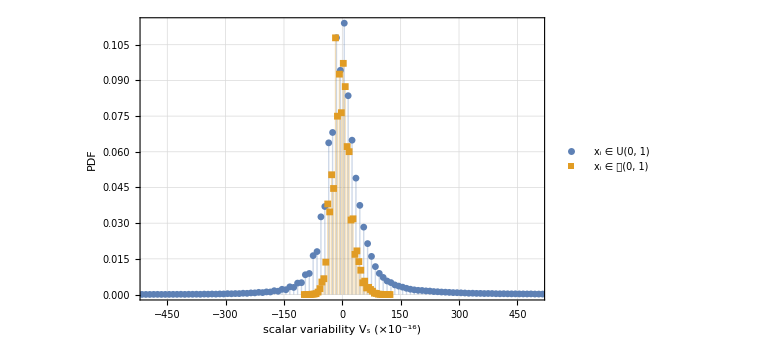

```mathematica
ListPlot[{{Differences[HistogramNormalV100[[1]]]/2+Drop[HistogramNormalV100[[1]],-1],HistogramNormalV100[[2]]/1000000}//Transpose,{Differences[HistogramUniformV100[[1]]]/2+Drop[HistogramUniformV100[[1]],-1],HistogramUniformV100[[2]]/1000000}//Transpose},PlotRange->{{-500,500},Full},PlotTheme->"Detailed",Filling->Axis,ImageSize->Large,FrameLabel->{"scalar variability V_s (×10^-16)","PDF"},PlotLegends->Placed[{"x_i ∈ U(0, 1)","x_i ∈ 𝒩(0, 1)"},{Right,Top}],LabelStyle->{FontSize->16},PlotMarkers->{Automatic,Small}]
(*Export["Histogram_scalar_variability_V100.pdf",ListPlot[{{Differences[HistogramNormalV100[[1]]]/2+Drop[HistogramNormalV100[[1]],-1],HistogramNormalV100[[2]]/1000000}//Transpose,{Differences[HistogramUniformV100[[1]]]/2+Drop[HistogramUniformV100[[1]],-1],HistogramUniformV100[[2]]/1000000}//Transpose},PlotRange->{{-500,500},Full},PlotTheme->"Detailed",Filling->Axis,ImageSize->Large,FrameLabel->{"scalar variability V_s (×10^-16)","PDF"},PlotLegends->Placed[{"x_i ∈ U(0,1)","x_i ∈ 𝒩(0, 1)"},{Right,Top}],LabelStyle->{FontSize->16},PlotMarkers->{Automatic,Small}]]*)
```

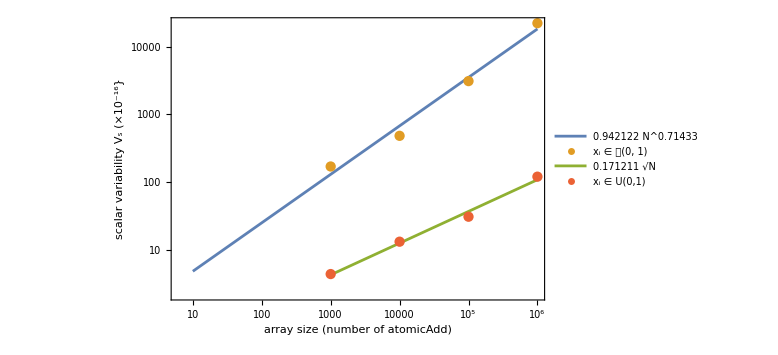

```mathematica
ListLogLogPlot[{Table[{10^i,10^gsNormalV100[i]},{i,1,6}],{{1000,10000,100000,1000000},Map[Max[Abs[#]]10^16&,V100data[[1,3;;6]]]}//Transpose,Table[{10^i,10^gsUniformV100[i]},{i,3,6}],{{1000,10000,100000,1000000},Map[Max[Abs[#]]10^16&,V100data[[2,3;;6]]]}//Transpose},Joined->{True,False,True,False},Frame->True,FrameLabel->{"array size (number of atomicAdd)","scalar variability V_s (×10^-16}"},PlotLegends->Placed[{N[10^gsNormalV100[N][[1]] N^(gsNormalV100[N][[2]][[1]]),3],"x_i ∈ 𝒩(0, 1)",N[10^gsUniformV100[N][[1]],3] √N,"x_i ∈ U(0,1)"},{Left,Top}],BaseStyle->{Font->"Arial",FontSize->16},ImageSize->Large,FrameTicks->{Automatic,{Map[If[(#==10)||(#==100)||(#==1000)||(#==10000)||(#==100000)||(#==1000000),{#,Column[{#,"("<>ToString[(IntegerPart[(#+64 - 1)/64])]<>")"}]},{#,""}]&,{10,20,30,40,50,60,70,80,90,100,200,300,400,500,600,700,800,900,1000,2000,3000,4000,5000,6000,7000,8000,9000,10000,20000,30000,40000,50000,60000,70000,80000,90000,100000,200000,300000,400000,500000,600000,700000,800000,900000,1000000}],None}}]
Export["scaling_relation_max_variability_v100.pdf",%];
```

```mathematica
Mi250X plots
```

```mathematica
{gsNormalMi250X,gsUniformMi250X,
gsUniformCenteredMi250X}={LinearModelFit[{Log10[NumElements[[3;;6]]],Map[Log10[Max[Abs[# 10^16]]]&,Mi250Xdata[[1,3;;6]]]}//Transpose,x,x]
,LinearModelFit[{Log10[NumElements[[3;;6]]],Map[Log10[Max[Abs[# 10^16]]]&,Mi250Xdata[[2,3;;6]]]}//Transpose,x,x]
,LinearModelFit[{Log10[NumElements[[3;;6]]],Map[Log10[Max[Abs[# 10^16]]]&,Mi250Xdata[[3,3;;6]]]}//Transpose,x,x]};
{HistogramNormalMi250X,
HistogramUniformMi250X,
HistogramUniformMi250X}={HistogramList[Mi250Xdata[[1,6]]*10^16,{10}],
HistogramList[Mi250Xdata[[2,6]]*10^16,{5}],HistogramList[Mi250Xdata[[2,6]]*10^16,{5}]};
```

## KL analysis

The  kl  analysis  is a quantity measuring how close two probabilities distributions are from each other. It is defined as ∫P(x) Log[P(x)/Q(x)]ⅆx. The discrete variant is defined as ∑_(i=1)^N p_i Log[p_i/q_i] . We compare the PDF of the scalar variability to the normal distribution and minimize the integral with respect to the mean and standard deviation. Calculations can be done analytically for the normal distribution and we find that the mean and standard deviation of the normal distribution that is the closest to the data are the mean and standard deviation extracted from the data.

```mathematica
KL[data_,binWidth_]:=Module[{tot,histo,mt,st,Ht,A,xi,i,expr,dv,s1,s2,Sol},
mt=Mean[data];
Ht=HistogramList[data,{binWidth},"PDF"];
st=StandardDeviation[data];
xi=Differences[Ht[[1]]]/2 + Drop[Ht[[1]],-1];
A=Map[PDF[NormalDistribution[μ,σ],#]&,xi];
dv=Ht[[2]]/( A);
expr=Sum[If[Ht[[2,i]]==0,0,Ht[[2,i]]Log[dv[[i]]]],{i,1,Length[dv]}];
s1=Simplify[D[expr,μ]];
s2=Simplify[D[expr,σ]];
Sol=Solve[{s1==0,s2==0},{μ,σ}];
Return[N[expr/.Sol[[2]]]]
]
```

```mathematica
Print["KL value for the V100"]
KL[V100DataForPlot[[1]]10^16,5]
Print["KL value for the Mi250X"]
KL[Mi250XDataForPlot[[1]]*10^16,25]
```

KL value for the V100

$Aborted

KL value for the Mi250X

$Aborted

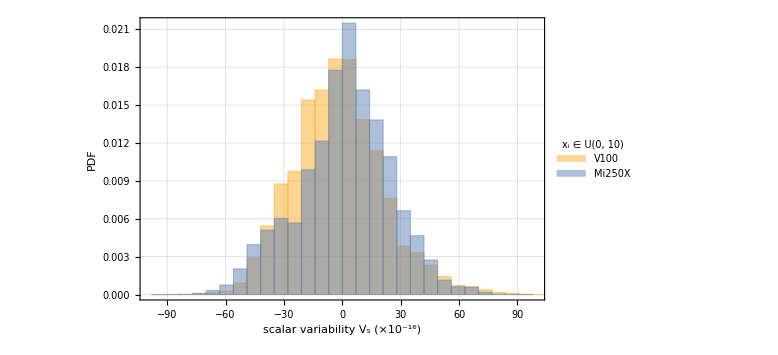

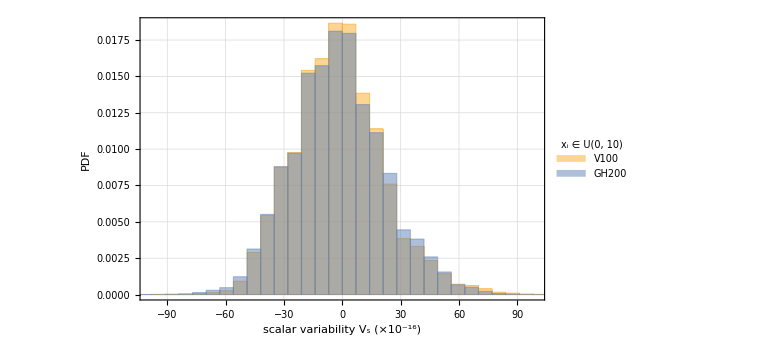

Difference_distribution_mi250x_v100_uniform_distribution.pdf

Difference_distribution_gh200_v100_uniform_distribution.pdf

Difference_distribution_mi250x_v100_uniform_distribution.png

Difference_distribution_gh200_v100_uniform_distribution.png

```mathematica
gV100Mi250X=Histogram[{V100DataForPlot[[2]],Mi250XDataForPlot[[2]]}10^16,{7},"PDF",PlotRange->{{-100,100},Automatic},Frame->True,PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{"scalar variability V_s (×10^-16)","PDF"},ChartLegends->Placed[{SwatchLegend[{"V100","Mi250X"},LegendFunction->"Frame",LegendLabel->Placed["x_i ∈ U(0, 10)",Above]],None},{Right,Top}],LabelStyle->{FontSize->16}]
gV100GH200=Histogram[{V100DataForPlot[[2]],GH200DataForPlot[[2]]}10^16,{7},"PDF",PlotRange->{{-100,100},Automatic},Frame->True,PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{"scalar variability V_s (×10^-16)","PDF"},
ChartLegends->Placed[{SwatchLegend[{"V100","GH200"},LegendFunction->"Frame",LegendLabel->Placed["x_i ∈ U(0, 10)",Above]],None},{Right,Top}],LabelStyle->{FontSize->16}]
(* Export the figures for the article and supplementary information *)
Export["figures/Difference_distribution_mi250x_v100_uniform_distribution.pdf",gV100Mi250X]
Export["figures/Difference_distribution_gh200_v100_uniform_distribution.pdf",gV100GH200]
Export["figures/Difference_distribution_mi250x_v100_uniform_distribution.png",gV100Mi250X]
Export["figures/Difference_distribution_gh200_v100_uniform_distribution.png",gV100GH200]
```

Draw  the PDF of the scalar variability for the V100 GPU

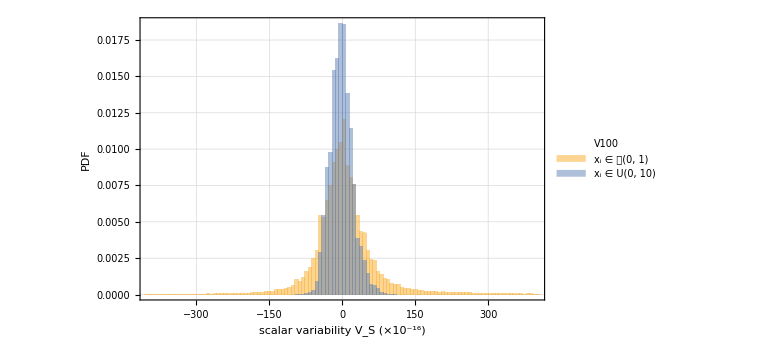

histogram_variability_v100.pdf

histogram_variability_v100.png

```mathematica
V100p=Histogram[{Select[V100DataForPlot[[1]]10^16,Abs[#]<400&],Select[V100DataForPlot[[2]]10^16,Abs[#]<400&]},{7},"PDF",PlotRange->{{-400,400},Automatic},Frame->True,ImageSize->Large,FrameLabel->{"scalar variability V_S (×10^-16)","PDF"},ChartLegends->Placed[{SwatchLegend[{"x_i ∈ 𝒩(0, 1)","x_i ∈ U(0, 10)"},LegendLabel->Placed["V100",Above],LegendFunction->Framed],None},{Right,Top}],LabelStyle->{FontSize->16},AxesLabel->{"×10^-16",None},GridLinesStyle->LightGray,GridLines->Automatic]
Export["figures/histogram_variability_v100.pdf",V100p]
Export["figures/histogram_variability_v100.png",V100p]
```

Draw  the PDF of the  scalar variability for the Mi250X GPU

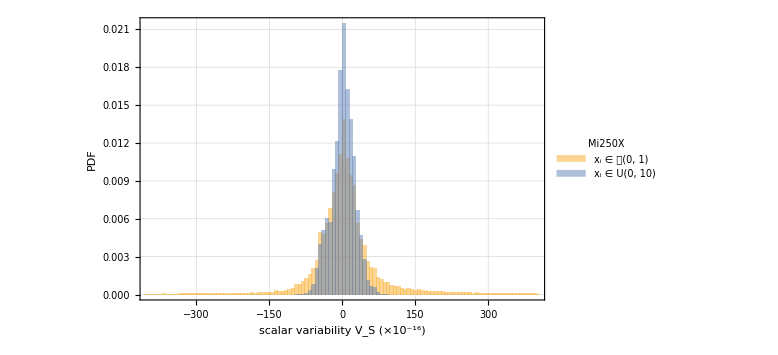

histogram_variability_mi250X.pdf

histogram_variability_mi250X.png

```mathematica
Mi250p=Histogram[{Select[Mi250XDataForPlot[[1]]10^16,Abs[#]<400&],Select[Mi250XDataForPlot[[2]]10^16,Abs[#]<400&]},{7},"PDF",PlotRange->{{-400,400},Automatic},Frame->True,PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{"scalar variability V_S (×10^-16)","PDF"},ChartLegends->Placed[{SwatchLegend[{"x_i ∈ 𝒩(0, 1)","x_i ∈ U(0, 10)"},LegendLabel->Placed["Mi250X",Above],LegendFunction->Framed],None},{Right,Top}],LabelStyle->{FontSize->16},AxesLabel->{"×10^-16",None}]
Export["figures/histogram_variability_mi250X.pdf",Mi250p]
Export["figures/histogram_variability_mi250X.png",Mi250p]
```

Draw  the PDF of the variability for the atomicAdd only implementation measured on the V100 GPU (500000 values only)

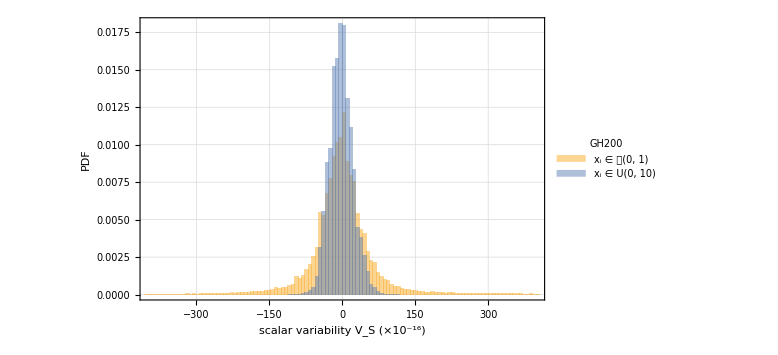

histogram_variability_gh200.pdf

histogram_variability_gh200.png

```mathematica
gh200p=Histogram[{Select[GH200DataForPlot[[1]]10^16,Abs[#]<400&],Select[GH200DataForPlot[[2]]10^16,Abs[#]<400&]},{7},"PDF",PlotRange->{{-400,400},Automatic},Frame->True,ImageSize->Large,FrameLabel->{"scalar variability V_S (×10^-16)","PDF"},ChartLegends->Placed[{SwatchLegend[{"x_i ∈ 𝒩(0, 1)","x_i ∈ U(0, 10)"},LegendLabel->Placed["GH200",Above],LegendFunction->Framed],None},{Right,Top}],LabelStyle->{FontSize->16},AxesLabel->{"×10^-16",None},GridLinesStyle->LightGray,GridLines->Automatic]
Export["figures/histogram_variability_gh200.pdf",gh200p]
Export["figures/histogram_variability_gh200.png",gh200p]
```

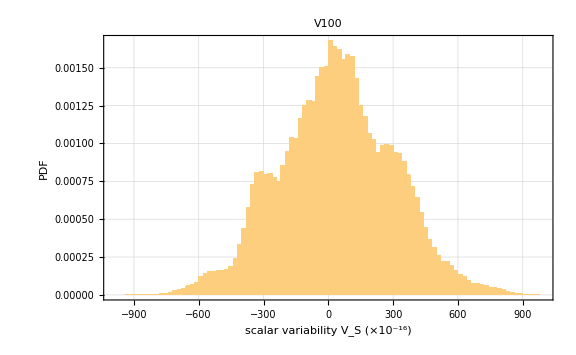

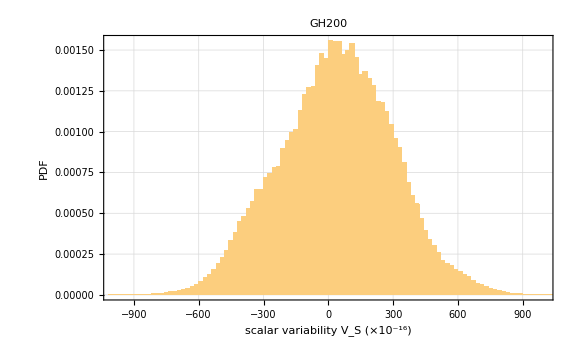

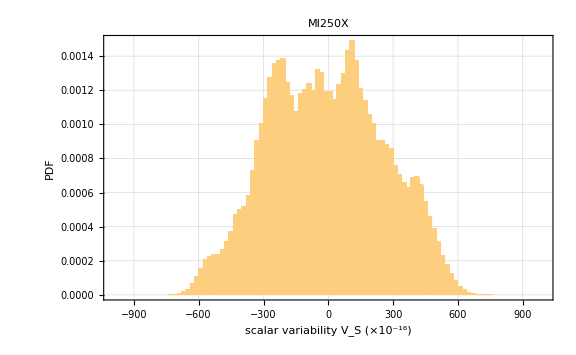

```mathematica
gAOV100=Histogram[AtomicAddOnlyV100[[6]] 10^16,{20},"PDF",PlotRange->{{-1000,1000},Automatic},Frame->True,PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{"scalar variability V_S (×10^-16)","PDF"},LabelStyle->{FontSize->16},PlotLabel->"V100"]
gAOGH200=Histogram[AtomicAddOnlyGH200[[6]] 10^16,{20},"PDF",PlotRange->{{-1000,1000},Automatic},Frame->True,PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{"scalar variability V_S (×10^-16)","PDF"},LabelStyle->{FontSize->16},PlotLabel->"GH200"]
gAOMi250x=Histogram[AtomicAddOnlMi2500[[6]] 10^16,{20},"PDF",PlotRange->{{-1000,1000},Automatic},Frame->True,PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{"scalar variability V_S (×10^-16)","PDF"},LabelStyle->{FontSize->16},PlotLabel->"MI250X"]
Export["figures/AO_method_uniform_distribution_1m_elements_V100.png",gAOV100];
Export["figures/AO_method_uniform_distribution_1m_elements_V100.pdf",gAOV100];
Export["figures/AO_method_uniform_distribution_1m_elements_Mi250x.png",gAOMi250x];
Export["figures/AO_method_uniform_distribution_1m_elements_Mi250x.pdf",gAOMi250x];
Export["figures/AO_method_uniform_distribution_1m_elements_GH200.png",gAOGH200];
Export["figures/AO_method_uniform_distribution_1m_elements_GH200.pdf",gAOGH200];
```

```mathematica
KL2[data_,binWidth_]:=Module[{tot,histo,mt,st,Ht,A,xi,i,expr,dv,s1,s2,Sol},
mt=Mean[data];
Ht=HistogramList[data,{binWidth},"PDF"];
st=StandardDeviation[data];
xi=Differences[Ht[[1]]]/2 + Drop[Ht[[1]],-1];
A=Map[PDF[NormalDistribution[mt,st],#]&,xi];
dv=Ht[[2]]/( A);
Return[Sum[If[Ht[[2,i]]==0,0,Ht[[2,i]]Log[dv[[i]]]],{i,1,Length[dv]}]];]
```

```mathematica
Table[KL2[V100DataForPlot[[1]]10^16,i],{i,1,50,2}]
Table[KL2[V100DataForPlot[[2]]10^16,i],{i,1,50,2}]
```

{2.78499,0.784942,0.466509,0.330972,0.257696,0.209499,0.177627,0.154155,0.135587,0.121554,0.109439,0.100074,0.092098,0.0852074,0.0794769,0.0735544,0.069161,0.065227,0.0616287,0.0584878,0.0553641,0.052792,0.0504196,0.0482389,0.046214}

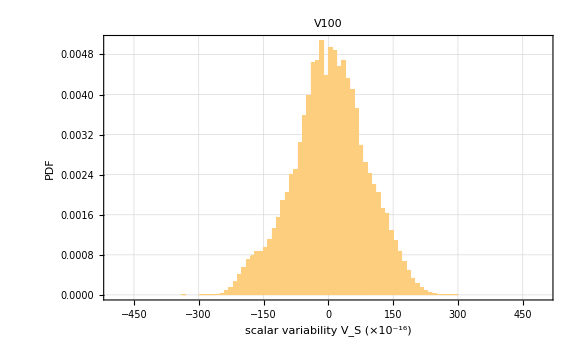

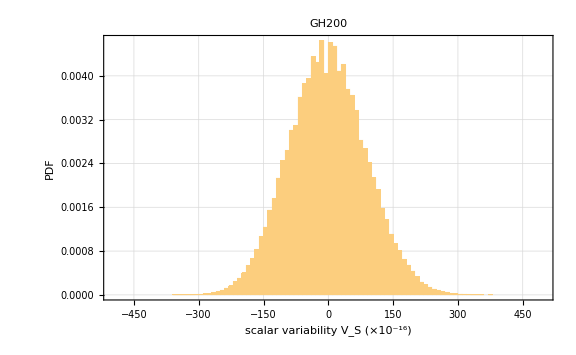

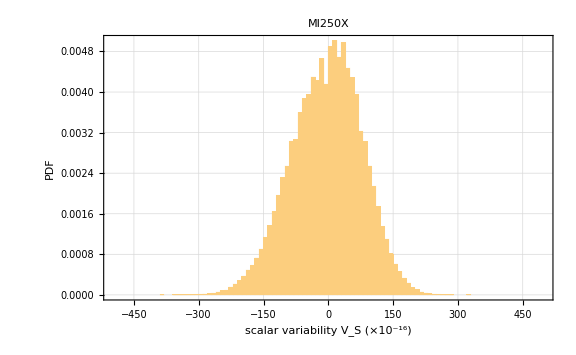

```mathematica
gAOV100=Histogram[AtomicAddOnlyV100[[5]] 10^16,{10},"PDF",PlotRange->{{-500,500},Automatic},Frame->True,PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{"scalar variability V_S (×10^-16)","PDF"},LabelStyle->{FontSize->16},PlotLabel->"V100"]
gAOGH200=Histogram[AtomicAddOnlyGH200[[5]] 10^16,{10},"PDF",PlotRange->{{-500,500},Automatic},Frame->True,PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{"scalar variability V_S (×10^-16)","PDF"},LabelStyle->{FontSize->16},PlotLabel->"GH200"]
gAOMi250x=Histogram[AtomicAddOnlMi2500[[5]] 10^16,{10},"PDF",PlotRange->{{-500,500},Automatic},Frame->True,PlotTheme->"Detailed",ImageSize->Large,FrameLabel->{"scalar variability V_S (×10^-16)","PDF"},LabelStyle->{FontSize->16},PlotLabel->"MI250X"]
Export["figures/AO_method_uniform_distribution_100k_elements_V100.png",gAOV100];
Export["figures/AO_method_uniform_distribution_100k_elements_V100.pdf",gAOV100];
Export["figures/AO_method_uniform_distribution_100k_elements_Mi250x.png",gAOMi250x];
Export["figures/AO_method_uniform_distribution_100k_elements_Mi250x.pdf",gAOMi250x];
Export["figures/AO_method_uniform_distribution_100k_elements_GH200.png",gAOGH200];
Export["figures/AO_method_uniform_distribution_100k_elements_GH200.pdf",gAOGH200];
```